# Patterns of the switch model in short, rot. symm. spherocylinder geometry

Params used for 2D rot. symm. simulation analysed here;
Note that the nonlinear reaction rates are scaled such that the fast-growth wild-type concentrations are 1000 um^-3.

```mathematica
params={
rhoD->varied,
rhoE->varied,
DD->16,
DE->10,
Dd->0.05,
Dde->0.05,
kD->0.3,
kdD->0.0015,
kdEr->1.5,
kdEl->10^-5,
kde->1,
λ->5,
μ->20,
L->varied,
he->0.5,
T->3000
};
```

## Setup

## Import of simulation data from Comsol

Import functions to load the data from Comsol simulations

```mathematica
NotebookEvaluate[NotebookDirectory[]<>"Comsol2Mathematica2hdf5.nb",
InsertResults->False,
EvaluationElements->"InitializationCell"
];
```

## Import Comsol data export and save as hdf5 file

```mathematica
data=Table[Import[NotebookDirectory[]<>"switchModel-spherocylinder2DRotSymm-rhoDE_1000_1500-differentLengths.txt","ComsolSweep1DMultiComp"],
{L,2,6}];
```

```mathematica
Do[
hdf5ExportSweep1D[NotebookDirectory[]<>"switchModel-spherocylinder2DRotSymm-rhoDE_1000_1500-L_"<>ToString[L]<>".h5",data[[L-1]],{}],
{L,2,6}];
```

## Analyze time-averaged profile

```mathematica
fastGrowthProfiles=Table[Block[{
kymo=data[[L-1]]["L"<>ToString[L]<>"rho1000"]["ud+ude"],
grid=data[[L-1]]["Grid"]-L/2},
Transpose[{grid,Mean@kymo}]
],{L,2,6}];
```

(No dynamic pattern formation in the 2 um long geometry with fast-growth concentrations)

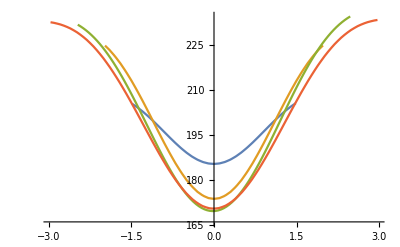

```mathematica
ListLinePlot[fastGrowthProfiles[[2;;]]]
```

```mathematica
slowGrowthProfiles=Table[Block[{
kymo=data[[L-1]]["L"<>ToString[L]<>"rho1500"]["ud+ude"],
grid=data[[L-1]]["Grid"]-L/2},
Transpose[{grid,Mean@kymo}]
],{L,2,6}];
```

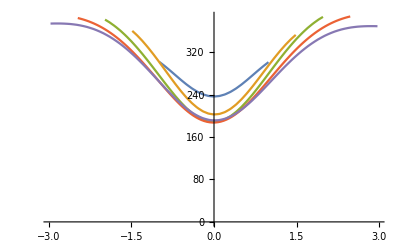

```mathematica
ListLinePlot[slowGrowthProfiles]
```

#### Measure full width at half maximum

```mathematica
fastGrowthWidths=Table[Block[{
profile=fastGrowthProfiles[[L-1]],
max,
min,
meanHeight,
interp,
intersection
},
{min,max}={Min@#,Max@#}&@profile[[All,2]];
meanHeight=Mean[{min,max}];
interp=Interpolation[profile];
intersection=x/.FindRoot[meanHeight==interp[x],{x,0.9}];
{
L,
2intersection
}
],
{L,2,6}];
```

```mathematica
slowGrowthWidths=Table[Block[{
profile=slowGrowthProfiles[[L-1]],
max,
min,
meanHeight,
interp,
intersection
},
{min,max}={Min@#,Max@#}&@profile[[All,2]];
meanHeight=Mean[{min,max}];
interp=Interpolation[profile];
intersection=x/.FindRoot[meanHeight==interp[x],{x,0.9}];
{
L,
2intersection
}
],
{L,2,6}];
```

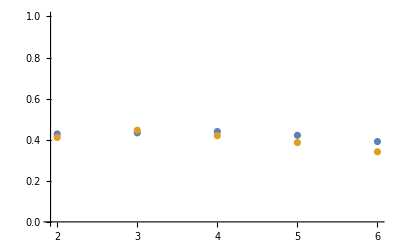

```mathematica
ListPlot[{{#[[1]],#[[2]]/(#[[1]]+1)}&/@fastGrowthWidths,{#[[1]],#[[2]]/(#[[1]]+1)}&/@slowGrowthWidths},PlotRange->{0,1}]
```